<<RQA`     Flip’s original usage

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

Graphs and measurements taken from the Webber Chapter are highlighted in green.

## Henon

The version in the Webber paper seems to be off by 30± iterations... (but note that the data in the file doesn’t seem to match this).

```mathematica
α=1.4;β=0.3;nMax=2000;settle=30;
```

```mathematica
henonxy=
Drop[RecurrenceTable[{x[n+1]==1-α x[n]^2+y[n],
y[n+1]==β x[n],x[0]==0.0,y[0]==0.0},{x,y},{n,1,nMax+settle},DependentVariables->{x,y}],settle];
```

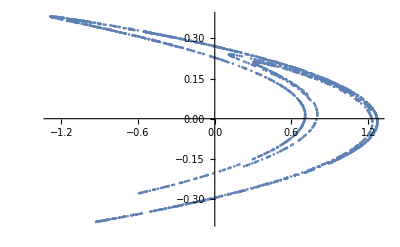

```mathematica
ListPlot[henonxy]
```

Convert into a time series

```mathematica
hts=TimeSeries[TemporalData[henonxy,{1,Automatic,1},ValueDimensions->2],ResamplingMethod->Automatic]
```

TimeSeries[…]

We’re dealing with a window 200-wide

```mathematica
tStart=1001;
w=200;
```

```mathematica
hw=TimeSeriesWindow[hts,{tStart,tStart+w-1}]
```

TimeSeries[…]

Make the 1D, x-only version

```mathematica
hx=TimeSeries[TemporalData[hw["Values"][[All,1]],{tStart,tStart+w-1,1}],ResamplingMethod->Automatic]
```

TimeSeries[…]

```mathematica
Export["~/Desktop/hcx",henonxy[[All,1]],"List"]
```

Export::nodir: Directory C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\~\Desktop\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\~\Desktop\hcx.

$Failed

```mathematica
Export["/hcx",henonxy[[All,1]],"List"]
```

OpenWrite::noopen: Cannot open C:\hcx.

$Failed

The plot from Webber

-Graphics-

and our data

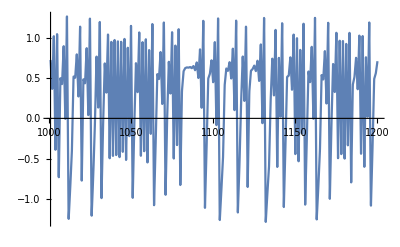

```mathematica
Plot[hx[t],{t,1001,1200}]
```

close... I had to shift the sequence by 30 cycles just to get the first ‘bursty’ section to align. There may be some more artifacts here and there. Notice the ‘bursty’ behavior around t=1050 in our data, but not in the Webber data. I tend to believe Mathematica’s numbers here. I have the data files from RQA141 and perhaps can re-create.

### Measures from my henon map

From the chapter:

Recurrence data computed from file HENCX using program RQD.EXE. RQA parameters: P1-Plast = 1001-1200; RANDSEQ = n; NORM = Euclid; DELAY = 1; EMBED = 3; RESCALE = max dist; RADUS = 3; COLORBND = 1; LINE = 2.

NB typo- I think he means ‘HENXC’ for the file name. Note that I’m not sure what RANDSEQ does here, as well as COLORBND. The RADIUS=3 doesn’t seem right, since points are (as you can see below) about a maximum of 3.0 units apart.

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

An unscaled distance map

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

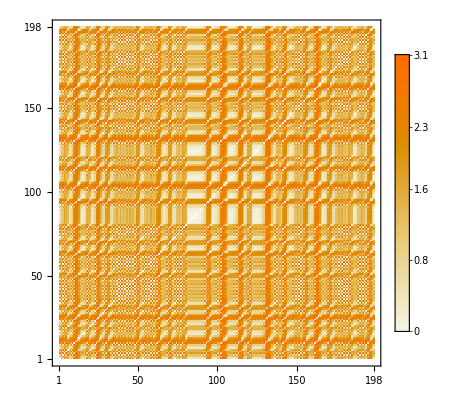

```mathematica
MatrixPlot[dm,DataReversed->True,PlotLegends->Automatic]
```

so, the RM claims that the ‘radius = 3’ but this really doesn’t make sense since that means that every point would be included... maybe it’s off by 100x?

Webber’s RM

-Graphics-

Mine looks similar but definitely not the same. There seems to be some crazy spatial / sampling thing going on maybe (note the ‘bracket’ squiggles at (1150,1050) on Webber and around (50,50 which is actually 1050,1050) in mine)

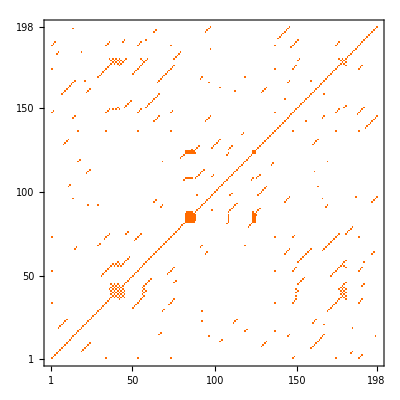

```mathematica
MatrixPlot[rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

From the chapter

%REC = 1.201; 
%DET = 88.703; 
LMAX = 12; 
ENT = 2.557; 
TND = –4.505; 
%LAM = 2.510; 
TT = 2.000.

#### Measures using my Henon calculations

Mine is not in % from personal preference. Off by .4% so I’m calling this a ‘match’.

```mathematica
RQARecurrence[rm]//N
```

0.0165103

Same with this

```mathematica
RQADeterminism[rm]//N
```

0.86646

Since LMAX is inversely proportional to the ‘chaos™’ in the system I’m returning it that way. Match.

```mathematica
RQAChaos[rm]//N
```

0.0833333

Entropy is close also.

```mathematica
RQAEntropy[rm]//N
```

2.5721

I think there’s a better way of calculating this w/o scaling the system up by 100,000 just to get a ‘pretty’ number. But- for the sake of what we have here, this is close.

```mathematica
RQATrend[rm]//N
```

-4.37716

I’m seeing a much greater laminarity here. 0.025 from the chapter...

```mathematica
RQALaminarity[rm]//N
```

0.111801

Similar with trapping time.

```mathematica
RQATrappingTime[rm]//N
```

4.5

In summary, everything is close-ish using the attractor I calculated. The laminarity is off, as well as the Trapping Time. Maybe this is due to my data?

### Measurements using Webber’s data file

I took the file HENXC from the RQA141 repository and turned it into the proper data structure.

```mathematica
whx=Import[NotebookDirectory[]<>"RQA141/HENXC","List"];
hx=TimeSeries[TemporalData[Take[whx,200],{tStart,tStart+w-1}],ResamplingMethod->Automatic]
```

Import::nffil: File not found during Import.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,200].

TemporalData::invstrct: The data TemporalData[Take[$Failed,200],{1001,1200}] is not a structurally valid TemporalData object.

TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic]

From the chapter-

-Graphics-

Alas, this data file doesn’t seem to be the above.

```mathematica
Plot[hx[x],{x,1001,1200}]
```

-Graphics-

Scrolling through, I can’t find a place where it ‘visually’ matches.

```mathematica
Manipulate[ListLinePlot[Take[whx,{x,x+199}]],{{x,1},1,801}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,200}].

ListLinePlot::lpn: Take[$Failed,{1,200}] is not a list of numbers or pairs of numbers.

This leads me to suspect the calculations?

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

MapThread::mptd: Object TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[«2»],{«2»}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,LessEqual[«2»]&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}] has only 0 of required 1 dimensions.

TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic]

A plot of the embedded function

```mathematica
ListPointPlot3D[Table[hxe3[t],{t,1001,1200,1}]]
```

Join::normal: Nonatomic expression expected at position 1 in Join[1001].

Join::normal: Nonatomic expression expected at position 1 in Join[1002].

Join::normal: Nonatomic expression expected at position 1 in Join[1003].

General::stop: Further output of Join::normal will be suppressed during this calculation.

-Graphics3D-

Note that the distance map is also different, the range of values is much greater, which is a little confusing.

```mathematica
MatrixPlot[dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance],DataReversed->True,PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[«2»],Rule[«2»]][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[Slot[«1»],«1»&]&)/@TimeSeries[TemporalData[Take[«2»],{«2»}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][«1»] at position 1 is not a matrix.

MatrixPlot[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0]],DataReversed→True,PlotLegends→Automatic]

```mathematica
Histogram[Flatten[dm]]
```

Histogram::ldata: TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[«2»],Rule[«2»]][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[Slot[«1»],«1»&]&)/@TimeSeries[TemporalData[Take[«2»],{«2»}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0] is not a valid dataset or list of datasets.

Histogram[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0]]

Lots of weird, spurious values out past 3.

And, again, the RM looks ‘similar’ but not the same.

```mathematica
MatrixPlot[rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

MatrixPlot::mat0: Argument Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[«2»][«1»]≤0,Message[MessageName[«2»]];,(Select[«2»]&)/@TimeSeries[TemporalData[«2»],Rule[«2»]][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-TimeSeries[TemporalData[MapThread[«1»&,{«2»}]],ResamplingMethod→Automatic][0]]]] at position 1 is not a matrix.

MatrixPlot[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0]]]],DataReversed→True]

#### Measures using HENXC

As a reminder

%REC = 1.201; 
%DET = 88.703; 
LMAX = 12; 
ENT = 2.557; 
TND = –4.505; 
%LAM = 2.510; 
TT = 2.000.

These measurements are also off, in some cases by a great amount, others, not so much

```mathematica
RQARecurrence[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQARecurrence[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQADeterminism[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQADeterminism[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQAChaos[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQAChaos[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQAEntropy[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQAEntropy[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQATrend[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQATrend[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQALaminarity[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQALaminarity[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQATrappingTime[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQATrappingTime[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.03-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,3,1.]&,{TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][PathFunction,All],If[-2.+TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162070&]&)/@TimeSeries[TemporalData[Take[$Failed,200],{1001,1200}],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

So- the best I can tell, I can’t get the same results with the Webber data as are presented in the paper. I can get results that are close, but, even using the data supplied with the RQA141 package my results vary from those presented.

## EMG

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts

```mathematica
emgC=Import["RQA141/EMGCONT","List"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
emgF=Import["RQA141/EMGFAT","List"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
ts=RQAMakeTimeSeries[emgC,1/1000.]
```

TemporalData::invstrct: The data TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0] is not a structurally valid TemporalData object.

TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic]

The focus is on the first 1972 points of the time series digitized at 1000 Hz (displayed from 37 ms to 1828 ms).

```mathematica
tsw=TimeSeriesWindow[ts,{.037,1.828}]
```

TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}]

```mathematica
Plot[tsw[t],{t,tsw["FirstTime"],tsw["LastTime"]},PlotRange->All]
```

Plot::plln: Limiting value TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][FirstTime] in {Charting`Private`pvar$162216,TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][FirstTime],TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]} is not a machine-sized real number.

Plot[tsw[t],{t,tsw[FirstTime],tsw[LastTime]},PlotRange→All]

```mathematica
ee=RQAEmbed[tsw,10,0.004];
```

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}] has only 0 of required 1 dimensions.

```mathematica
MatrixPlot[dm=RQADistanceMap[ee,DistanceFunction->EuclideanDistance],DataReversed->True,PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[«2»],{«2»}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[Slot[«1»],«1»&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][«1»] at position 1 is not a matrix.

MatrixPlot[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]],DataReversed→True,PlotLegends→Automatic]

```mathematica
MinMax[dm]
```

{TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]],TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]}

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

Histogram::ldata: Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[«2»][«1»]≤0,Message[MessageName[«2»]];,(Select[«2»]&)/@TimeSeriesWindow[TimeSeries[«2»],{«2»}][TimeList]]}]],ResamplingMethod→Automatic][0]] is not a valid dataset or list of datasets.

Histogram[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]]

```mathematica
MatrixPlot[rm=RQARecurrenceMap[ee,0.05,"Rescale"->True,DistanceFunction->EuclideanDistance],DataReversed->True]
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

MatrixPlot::mat0: Argument Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[«2»][«1»]≤0,Message[MessageName[«2»]];,(Select[«2»]&)/@TimeSeriesWindow[TimeSeries[«2»],{«2»}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-TimeSeries[TemporalData[MapThread[«1»&,{«2»}]],ResamplingMethod→Automatic][0]]]] at position 1 is not a matrix.

MatrixPlot[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]]],DataReversed→True]

```mathematica
RQARecurrence[rm]*100.0
```

100. RQARecurrence[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]]]]

```mathematica
RQADeterminism[rm]*100.0
```

100. RQADeterminism[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]]]]

```mathematica
1.0/RQAChaos[rm]
```

1./RQAChaos[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0]]]]]

```mathematica
RQAEntropy[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQAEntropy[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQATrend[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQATrend[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
RQATrappingTime[rm]//N
```

Rescale::nargs: If the first argument is not a list or a SparseArray, two or three arguments are expected.

RQATrappingTime[Rescale[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][HeavisideTheta[0.05-1. TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,10,0.004]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-0.036+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162228&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic][0.]]]]]

```mathematica
ts["Properties"]
```

TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Properties]

```mathematica
Mean[Differences[ts["Times"]]]
```

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]].

Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]

```mathematica
f=CorrelationFunction[ts,{1,100}]
```

CorrelationFunction[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1,100}]

```mathematica
Plot[f[t],{t,1,100},PlotRange->All]
```

-Graphics-

```mathematica
FindRoot[f[t],{t,1}]
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,100.}][1.]} is not a list of numbers with dimensions {1} at {t} = {1.}.

FindRoot[f[t],{t,1}]

```mathematica
embedLag=RQAEstimateLag[ts]
```

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]].

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]

```mathematica
RQAEstimateDimensionality[ts,embedLag]
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nearest::near1: TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values] is neither a list of real points nor a valid list of rules.

Flatten::fldep: Level 3 specified in {{3,4}} exceeds the levels, 1, which can be flattened together in TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]].

MapThread::mptd: Object TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]] at position {2, 1} in MapThread[If[Length[#1]==1,#1,DeleteCases[#1,#2]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]],{1}}] has only 0 of required 1 dimensions.

MapThread::list: List expected at position 2 in MapThread[#1,TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]].

Part::pkspec1: The expression MapThread[#1,TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]] cannot be used as a part specification.

MapThread::mptd: Object TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values] at position {2, 1} in MapThread[SquaredEuclideanDistance,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values]⟦MapThread[#1,TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[«3»],Rule[«2»]][Values],DistanceFunction→SquaredEuclideanDistance][{{«1»}},{}]]]⟧}] has only 0 of required 1 dimensions.

10 Mean[MapThread[SquaredEuclideanDistance,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values]⟦MapThread[#1,TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]]⟧}]]

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,LessEqual[«2»]&]&)/@«1»]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

Nearest::near1: TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[«1»]/.FindRoot[RQA`Private`f$162445[«1»],{«4»}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[Times[«2»]+TimeSeries[«2»][«1»]≤0,Message[MessageName[«2»]];,(Select[«2»]&)/@TimeSeries[TemporalData[«3»],Rule[«2»]][TimeList]]}]],ResamplingMethod→Automatic][Values] is neither a list of real points nor a valid list of rules.

General::stop: Further output of Nearest::near1 will be suppressed during this calculation.

Flatten::fldep: Level 3 specified in {{3,4}} exceeds the levels, 1, which can be flattened together in TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[«1»]/.FindRoot[RQA`Private`f$162445[«1»],{«4»}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[Times[«2»]+TimeSeries[«2»][«1»]≤0,Message[MessageName[«2»]];,(Select[«2»]&)/@TimeSeries[TemporalData[«3»],Rule[«2»]][TimeList]]}]],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[Slot[«1»],Slot[«1»],2,ReplaceAll[«2»]]&,{«1»,If[«1»]}]],«1»][Values],«1»][«1»]].

MapThread::list: List expected at position 2 in MapThread[#1,TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,Times[«2»]/.FindRoot[«2»]]&,{TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic][PathFunction,All],If[Plus[«2»]≤0,Message[«1»];,(«1»&)/@TimeSeries[«2»][«1»]]}]],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[«4»]&,{TimeSeries[«2»][«2»],If[«3»]}]],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]].

General::stop: Further output of MapThread::list will be suppressed during this calculation.

Part::pkspec1: The expression MapThread[#1,TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,Times[«2»]/.FindRoot[«2»]]&,{TimeSeries[TemporalData[$Failed,{«3»},Rule[«2»]],ResamplingMethod→Automatic][PathFunction,All],If[Plus[«2»]≤0,Message[«1»];,(«1»&)/@TimeSeries[«2»][«1»]]}]],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[«4»]&,{TimeSeries[«2»][«2»],If[«3»]}]],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Null,{{{2,0.,2,Mean[MapThread[SquaredEuclideanDistance,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values]⟦MapThread[#1,TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]]⟧}]],2,Mean[MapThread[SquaredEuclideanDistance,{TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[-(RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}])+TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162523&]&)/@TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][Values],TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[-(RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}])+TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162523&]&)/@TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][Values]⟦MapThread[#1,TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[-(RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}])+TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162523&]&)/@TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][Nearest[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][PathFunction,All],If[-(RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}])+TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$162523&]&)/@TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][TimeList]]}]],ResamplingMethod→Automatic][Values],DistanceFunction→SquaredEuclideanDistance][{{1}},{}]]]⟧}]]}}}}

```mathematica
e=RQATimeSeriesEpochs[tsw,1,0.25]
```

Table::iterb: Iterator {RQA`Private`t0,TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][FirstTime],-1+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime],0.25} does not have appropriate bounds.

Table[TimeSeriesWindow[TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}],{RQA`Private`t0,RQA`Private`t0+1}],{RQA`Private`t0,TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][FirstTime],-1+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime],0.25}]

```mathematica
e1=RQAEmbed[tsw,2,embedLag];
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
cNeighbors[ts_,OptionsPattern[]]:=Module[{nf},
	nf=Nearest[ts["Values"]];
	Position[ts["Values"],#]&/@ts["Values"]]
```

```mathematica
cNeighbors[tsw]
```

Nearest::near1: TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][Values] is neither a list of real points nor a valid list of rules.

TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][{{1}}]

```mathematica
d2=RQANeighborDistances[tsw,n]
```

RQANeighborDistances[TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}],n]

```mathematica
d1=RQANeighborDistances[e1,n]
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

RQANeighborDistances[TimeSeries[TemporalData[MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(RQA`Private`t$162445 Mean[Differences[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic][Times]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}])+TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][LastTime]≤0,Message[RQAEmbed::truncated];,(Select[#1,#1≤RQA`Private`truncTime$221976&]&)/@TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][TimeList]]}]],ResamplingMethod→Automatic],n]

```mathematica
neighborDistanceChange[d1_,d2_]:=MapThread[If[#1==0,0,Sqrt[(#2-#1)/#1]]&,{d1,d2}]
```

```mathematica
neighborDistanceChange[d1_,d2_]:=MapThread[Norm[{##}]&,{d1,d2}]
```

```mathematica
falseNeighborP[d1_,d2_,thresh_:10]:=Module[{d},
	d=neighborDistanceChange[d1,d2];
	N[Count[d,x_/;x>thresh]/Length[d2]]
]
```

```mathematica
d=neighborDistanceChange[d1,d2];
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
Count[d,x_/;x>.1]
```

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

FindRoot::nlnum: The function value {CorrelationFunction[TimeSeriesResample[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{1.,1.,1.}],{1.,0.}][2.]} is not a list of numbers with dimensions {1} at {RQA`Private`t$162445} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

MapThread::mptd: Object TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All] at position {2, 1} in MapThread[RQA`Private`embedHelper[#1,#2,2,RQA`Private`t$162445 Mean[Differences[TimeSeries[«2»][«1»]]]/.FindRoot[RQA`Private`f$162445[RQA`Private`t$162445],{RQA`Private`t$162445,2,1,RQA`Private`smax$162445}]]&,{TimeSeriesWindow[TimeSeries[TemporalData[$Failed,{0,Automatic,0.001},ValueDimensions→0],ResamplingMethod→Automatic],{0.037,1.828}][PathFunction,All],If[-(Times[«2»]/.FindRoot[«2»])+TimeSeriesWindow[TimeSeries[TemporalData[«3»],Rule[«2»]],{0.037,1.828}][LastTime]≤0,«1»;,(Select[#1,LessEqual[«2»]&]&)/@TimeSeriesWindow[«1»,{0.037,«6»}][T…t]]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

0